### Module :

```mathematica
sensitivity[odeVecRHS_,ICs_,paramVals_,tMax_]:=Module[{pg=12,numVars,numParams,p,x,t,pList,pListRR,xList,xListFunc,sol,sensitivityMRaw,solRaw},
numVars=Length[ICs];
numParams=Length[paramVals];
pList=p/@Range[numParams]; (* {p[1],p[2],...} *)
pListRR=MapThread[Rule,{pList,paramVals}];(* see below *)
xList=x/@Range[numVars];(* {x[1],x[2],...} *)
xListFunc[t_]=x[#][t]&/@Range[numVars];(* {x[1][t],x[2][t],...} *)
sol=ParametricNDSolve[
{xListFunc'[t]==odeVecRHS@@Join[xListFunc[t],pList](*see below*),xListFunc[0]==ICs},
xList,{t,tMax},pList,
PrecisionGoal->pg];
sensitivityMRaw=D[#@@pList&/@xList(*see below*),{pList}]/.sol/.pListRR;
solRaw=#@@paramVals&/@xList/.sol;
{
Function[t,Evaluate[Map[#[t]&,sensitivityMRaw,{2}]]],
Function[t,Evaluate[(Transpose@Outer[Divide,paramVals,Map[#[t]&,solRaw]]) Map[#[t]&,sensitivityMRaw,{2}]]]
}
]
```

```mathematica
parameterNames=ToString@@@{rN,r1,kC,kN,k2,a,b,γB,rB};
sensitivityExample[num_,s_]:=sensitivity[
Function[{n,c,B,rN,r1,kC,kN,k2,a,b,gammaB,rB},{
-rN n Log[(n+c)/kN],
-((b(n+c-kN)^2)/(a(n+c)^2+((n+c)-kN)^2)+r1 )c Log[(n+c)/kC],
rB B-gammaB B k2 c/(1+k2 c)
}](*pure function for dependent variables and paramters together*),
{6.0,0.36,94.84}(*initial conditions*),{0.17,0.037,139.28,500.0,0.247,0.423,0.525,1.15,0.065}(*parameter values*),200(*final t value*)
][[num]][s];(*the s here and in sensitivityExample[s_] can be any variable of your choosing*)
```

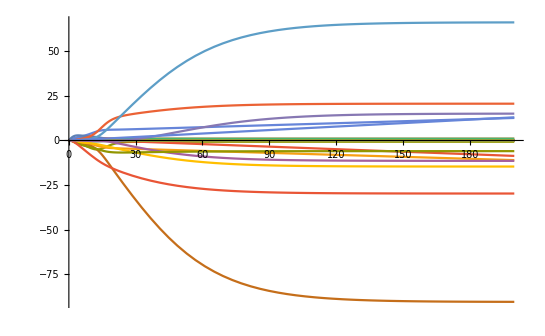

```mathematica
Plot[sensitivityExample[2,t]//Flatten//Evaluate,{t,0,200},PlotRange->All]
```

```mathematica
rankParameters[num_]:=Module[
{L2Norm,listVarNorm},
L2Norm=Total[NIntegrate[sensitivityExample[num,t]^2,{t,0,200},AccuracyGoal->10]];
listVarNorm={#,parameterNames[[#]],L2Norm[[#]]/Max[L2Norm]}&/@Range[Length[parameterNames]];
listVarNorm=Reverse[SortBy[listVarNorm,#[[-1]]&]]
];
```

```mathematica
ranked=rankParameters[2];
```

```mathematica
parameterNames
```

{rN,r1,kC,kN,k1,k2,a,b,γB,rB}

```mathematica
ranked
```

{{3,kC,1.},{4,kN,0.528741},{8,γB,0.122186},{1,rN,0.059527},{5,k2,0.0269864},{2,r1,0.0264314},{6,a,0.0159609},{9,rB,0.00958021},{7,b,0.00612151}}

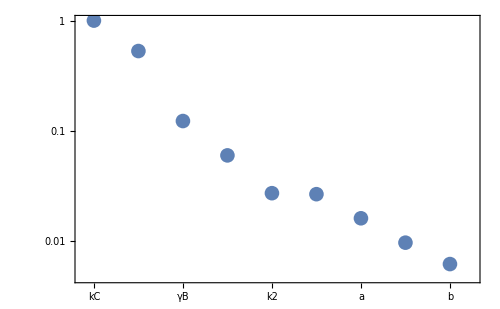

```mathematica
rankedPlot = ListLogPlot[ranked[[;;,-1]],Frame->True,
FrameTicks->{{All,None},{{#,ranked[[#,2]]}&/@Range[Length[parameterNames]],None}},
Axes->False,
PlotRange->{{0.75,9.5},All},
GridLines->{{},{1*^-4}},
GridLinesStyle->Red,
FrameStyle->Directive[Thickness[0.0035],Black],
LabelStyle->{FontSize->18,Black,FontFamily->"Arial"},
PlotMarkers->{Automatic,15},
ImageSize->500]
```

```mathematica
(* Next we would like to systematically parse the parameters and remove k heavily correlated parameters and p-k remaining parameters. Since all parameters are sensitive, we look for correlations.  *)
computeCorrelatedSet[sensitivityMatrix0_,paramSet_,cutoff_]:=Module[
{sensitivityMatrix,preCovariance,nParams,Id,covariance,correlation,upper},

nParams=Length[paramSet];
(* Order the columns so the most sensitive parameter is first *)
sensitivityMatrix=sensitivityMatrix0[[;;,ranked[[paramSet,1]]]];

preCovariance=Transpose[sensitivityMatrix].sensitivityMatrix;
Id=IdentityMatrix[nParams];

(* In case the matrix is badly conditioned, we solve for each column and build the covariance matrix in this fashion *)
covariance=Table[LinearSolve[preCovariance,Id[[i]],Method->"Cholesky"],{i,nParams}];
correlation=Table[covariance[[i,j]]/(√(covariance[[i,i]]covariance[[j,j]])),{i,Length[covariance]},{j,Length[covariance]}];

upper=UpperTriangularize[correlation,1];

{{Max[Abs[upper]]≥cutoff,Position[Abs[upper],Max[Abs[upper]]][[1]]},correlation,covariance}

];
obtainIdentifiableParameters[cutoff_]:=Module[
{sensitivityMatrix0,sensitivityMatrix,preCovariance,nParams,sensitiveParams,insensitiveParams,correlation,covariance,correlatedSet,kSensParams},

sensitivityMatrix0=Flatten[sensitivityExample[1,Range[0,200,0.01]],{{1,3},{2}}];
nParams=Length[parameterNames];
sensitiveParams=Range[nParams];
insensitiveParams=Complement[Range[nParams],sensitiveParams];
Print["Remaining sensitive parameters ",ranked[[sensitiveParams,2]]];

{correlatedSet,correlation,covariance}=computeCorrelatedSet[sensitivityMatrix0,sensitiveParams,cutoff];

If[correlatedSet[[1]],
{
Print[ranked[[sensitiveParams[[correlatedSet[[2]]]],2]], " are correlated with magnitude ", Part@@Prepend[correlatedSet[[2]],correlation],"..."];
sensitiveParams=Delete[sensitiveParams,correlatedSet[[2,2]]];
Print["Remaining sensitive parameters ",ranked[[sensitiveParams,2]]];
}];

insensitiveParams=Complement[Range[nParams],sensitiveParams];

(* Begin the do while loop which iteratively removes correlated parameters that are less sensitive *)
n=0;
While[correlatedSet[[1]],
{

(* We grab the remaining sensitive parameters and redo the correlation analysis *)
{correlatedSet,correlation,covariance}=computeCorrelatedSet[sensitivityMatrix0,sensitiveParams,cutoff];
If[correlatedSet[[1]],
{
Print[ranked[[sensitiveParams[[correlatedSet[[2]]]],2]], " are correlated with magnitude ", Part@@Prepend[correlatedSet[[2]],correlation],"..."];
sensitiveParams=Delete[sensitiveParams,correlatedSet[[2,2]]];
Print["Remaining sensitive parameters ",ranked[[sensitiveParams,2]]];
}];
insensitiveParams=Complement[Range[nParams],sensitiveParams];
}
];

{sensitiveParams,correlatedSet,sensitivityMatrix0}

];
```

```mathematica
test=obtainIdentifiableParameters[0.9];
```

Remaining sensitive parameters {kC,kN,γB,rN,k2,r1,a,rB,b}

{k2,rB} are correlated with magnitude 0.936571...

Remaining sensitive parameters {kC,kN,γB,rN,k2,r1,a,b}

{γB,k2} are correlated with magnitude -0.960726...

Remaining sensitive parameters {kC,kN,γB,rN,r1,a,b}

```mathematica
test[[3]]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.},60001,{0.000606306,0.00203171,-3.24553×10^-6,6.61656×10^-7,-0.000295538,-0.000135002,-0.0000568417,-0.0001292,0.000998549}}
 |  |  |  |

```mathematica
{correlationMatrix,covarianceMatrix}=computeCorrelatedSet[test[[3]],Range[9],0.9][[2;;3]];
```

```mathematica
parameterNames
covarianceMatrix//MatrixForm
```

{rN,r1,kC,kN,k2,a,b,γB,rB}

(0.0273541 | 0.0000708947 | 0.0000418608 | -2.40851×10^-7 | 0.0000794598 | -0.0000197986 | -0.000806978 | 0.0000400925 | -0.0000915471
0.0000708947 | 0.0000774089 | 2.92299×10^-7 | -4.43332×10^-8 | 4.38385×10^-7 | -1.94981×10^-6 | -5.98988×10^-6 | 2.27342×10^-7 | 1.4237×10^-6
0.0000418608 | 2.92299×10^-7 | 0.0000683262 | -7.68968×10^-9 | -0.0000514406 | -4.31093×10^-8 | -1.45587×10^-6 | -0.0000212084 | -2.34107×10^-7
-2.40851×10^-7 | -4.43332×10^-8 | -7.68968×10^-9 | 7.29365×10^-10 | -8.38632×10^-9 | 3.72841×10^-9 | 5.17678×10^-8 | -4.59299×10^-9 | 5.18155×10^-9
0.0000794598 | 4.38385×10^-7 | -0.0000514406 | -8.38632×10^-9 | 0.0000674178 | -7.89535×10^-8 | -2.66309×10^-6 | 0.0000396712 | -3.5034×10^-7
-0.0000197986 | -1.94981×10^-6 | -4.31093×10^-8 | 3.72841×10^-9 | -7.89535×10^-8 | 2.85819×10^-7 | 2.03709×10^-6 | -4.00167×10^-8 | -1.84421×10^-7
-0.000806978 | -5.98988×10^-6 | -1.45587×10^-6 | 5.17678×10^-8 | -2.66309×10^-6 | 2.03709×10^-6 | 0.0000390721 | -1.34973×10^-6 | 1.5621×10^-6
0.0000400925 | 2.27342×10^-7 | -0.0000212084 | -4.59299×10^-9 | 0.0000396712 | -4.00167×10^-8 | -1.34973×10^-6 | 0.0000266131 | -1.82298×10^-7
-0.0000915471 | 1.4237×10^-6 | -2.34107×10^-7 | 5.18155×10^-9 | -3.5034×10^-7 | -1.84421×10^-7 | 1.5621×10^-6 | -1.82298×10^-7 | 6.46042×10^-7)

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
FindRoot[{OneSidedPValue/.StudentTPValue[x,2]}==0.025,{x,2.3}]
```

{x→4.30265}

```mathematica
4.30265 √(0.13622856/2)√covarianceMatrix[[1,1]]
```

0.185723

```mathematica
optimal={0.17,0.037,139.28,500.0,0.247,0.423,0.525,1.15,0.065};
```

```mathematica
Table[{optimal[[i]]-4.30265 √(0.13622856/2)√covarianceMatrix[[i,i]],optimal[[i]]+4.30265 √(0.13622856/2)√covarianceMatrix[[i,i]]},{i,9}]
```

{{-0.0157234,0.355723},{0.0271201,0.0468799},{139.271,139.289},{500.,500.},{0.23778,0.25622},{0.4224,0.4236},{0.517981,0.532019},{1.14421,1.15579},{0.0640974,0.0659026}}

```mathematica
parameterNames
correlationMatrix//MatrixForm
```

{rN,r1,kC,kN,k2,a,b,γB,rB}

(1. | 0.04872 | 0.0306198 | -0.0539217 | 0.0585125 | -0.223912 | -0.780579 | 0.0469899 | -0.688657
0.04872 | 1. | 0.00401919 | -0.186578 | 0.00606838 | -0.414526 | -0.108915 | 0.00500883 | 0.201323
0.0306198 | 0.00401919 | 1. | -0.0344463 | -0.757923 | -0.00975509 | -0.0281771 | -0.497355 | -0.0352363
-0.0539217 | -0.186578 | -0.0344463 | 1. | -0.0378191 | 0.258229 | 0.306658 | -0.0329667 | 0.238702
0.0585125 | 0.00606838 | -0.757923 | -0.0378191 | 1. | -0.0179862 | -0.0518878 | 0.936571 | -0.053085
-0.223912 | -0.414526 | -0.00975509 | 0.258229 | -0.0179862 | 1. | 0.60958 | -0.0145093 | -0.429174
-0.780579 | -0.108915 | -0.0281771 | 0.306658 | -0.0518878 | 0.60958 | 1. | -0.041857 | 0.310919
0.0469899 | 0.00500883 | -0.497355 | -0.0329667 | 0.936571 | -0.0145093 | -0.041857 | 1. | -0.0439647
-0.688657 | 0.201323 | -0.0352363 | 0.238702 | -0.053085 | -0.429174 | 0.310919 | -0.0439647 | 1.)